{{100,1.21},{150,1.44},{200,2.11},{250,2.25},{300,2.56}}

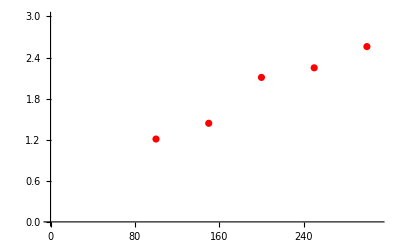

```mathematica
X = {100,150,200,250,300};
y = {1.21,1.44,2.11,2.25,2.56};
n = Length[X];
combinedData = Table[{X[[i]],y[[i]]},{i,1,n,1}]
pltPoints = ListPlot[combinedData,PlotRange->{{0,310},{0,3}}, PlotStyle->{Red,Thick}]
```

## Line using formula

```mathematica
XiYi = Table[{X[[i]] * y[[i]]} , {i,1,n,1}];
Xi2 = Table[{X[[i]]^2} , {i,1,n,1}];
m = (n* Total[XiYi] - Total[X]*Total[y])/(n * (Total[Xi2])- Total[X]^2);
m = m[[1]]
c = (Total[y]*Total[Xi2] - Total[X]*Total[XiYi])/(n * (Total[Xi2])- Total[X]^2);
c = c[[1]]
```

0.00702

0.51

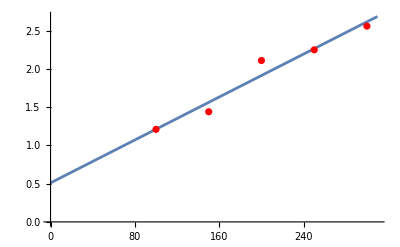

```mathematica
datatest = Table[{x , m * x + c}, {x,0,310,1}];
pltLine = ListLinePlot[datatest];
Show[pltLine,pltPoints]
```

## Using Linear model fit

## multi parameter data

```mathematica
Clear["Global`*"]
θ = {90,87,84,81,78.5,76,73.5,71.2,69,67,65,62.2,61,60,58.5,57.2,56.6,56,55.2,54.7};
t = Table[time,{time,0,9.5,0.5}];
combinedData = Table[{ t[[i]], θ[[i]]} , {i,1,20,1}];
```

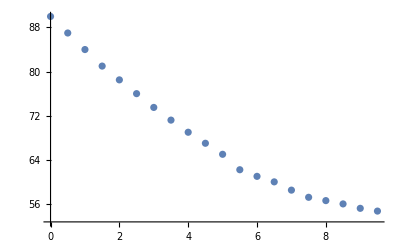

```mathematica
pltPoints = ListPlot[combinedData]
```

{a1→166.113,a2→-110.175,a3→38.2371}

38.2371-110.175 ⅇ^-x+166.113/(1+x)

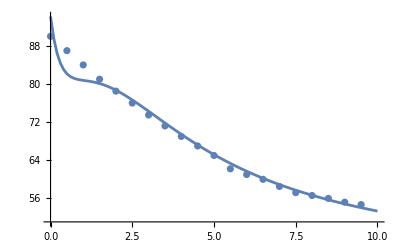

```mathematica
params = FindFit[combinedData,a1/(x+1)  + a2 Exp[-x] + a3 , {a1,a2,a3} , x]
FitCurve[x_] = a1/(x+1)  + a2 Exp[-x] + a3 /. params
pltCurve = ListLinePlot[Table[{x,FitCurve[x]} , {x,0,10,0.1}]];
Show[pltCurve,pltPoints]
```

{166.113,-110.175,38.2371}

38.2371-110.175 ⅇ^-x+166.113/(1+x)

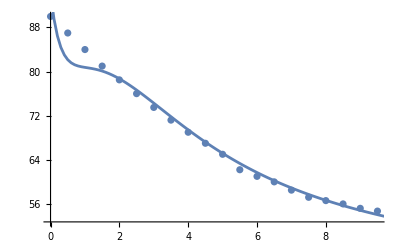

```mathematica
paramMatrix = Table[{1/(t[[i]]+1),  Exp[-t[[i]]] , 1} , {i,1,20,1}];
{a1,a2,a3} = LinearSolve[Transpose[paramMatrix].paramMatrix , Transpose[paramMatrix].θ]
LinearFitCurve[x_] = a1/(x+1) + a2 Exp[-x] + a3
pltCurveLinear = ListLinePlot[Table[{x,LinearFitCurve[x]} , {x,0,10,0.1}]];
Show[pltPoints,pltCurveLinear]
```

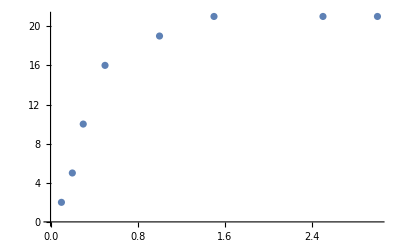

```mathematica
Clear["Global`*"]
X = {0.1,0.2,0.3,0.5,1,1.5,2.5,3};
y = {2,5,10,16,19,21,21,21};
combined = Table[{X[[i]] , y[[i]]} , {i,1,8,1}];
pltPoints = ListPlot[combined]
```

FittedModel[19.2895 ⅇ^(-0.0972941 x)+7.93789 Log[x]+2.02666 Sin[1.64462 x]]

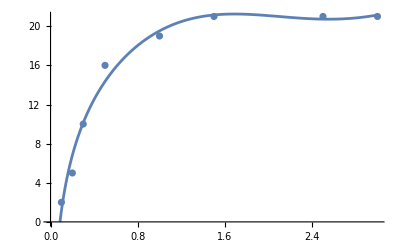

```mathematica
NonLinearFunc =NonlinearModelFit[combined,a Log[x] + b Exp[- c x] + e Sin[d x], {a,b,c,d,e} , x]
pltNonLinear = ListLinePlot[Table[{x,NonLinearFunc[x]},{x,0,3,0.01}]];
Show[pltPoints,pltNonLinear]
```